```mathematica
changepoint=0.451985;
```

```mathematica
λ[t_]:=Piecewise[{{1,t<changepoint},{2,t≥changepoint}}]
```

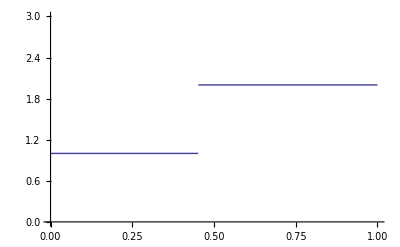

```mathematica
Plot[λ[t],{t,0,1},PlotRange->{0,3}]
```

```mathematica
ts={0,0.095310,0.200671,0.318454,0.451985,0.606136,0.788457,1.011601,1.299283,1.704748,2.397895,Infinity};
```

```mathematica
n=Length[ts]-2;
```

```mathematica
t[i_]:=ts[[i+1]];
```

```mathematica
Omega[t1_,t2_]:=Integrate[1/λ[s],{s,t1,t2}]
```

```mathematica
(*Pi*)
```

```mathematica
pi[i_,j_]:=Piecewise[{
{3/2*Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])(1-Exp[-Omega[t[j],t[j+1]]]),0<=i<j≤n&&(i∈Integers&&j∈Integers)},
{1/2 Exp[-3Omega[0,t[i]]](2-3Exp[-(t[i+1]-t[i])/λ[t[i]]]+Exp[-3(t[i+1]-t[i])/λ[t[i]]]),
0≤i==j≤n&&(i∈Integers&&j∈Integers)}}]
```

```mathematica
(*Pi is working, at least for constant N [λ]*)
```

```mathematica
(*E[t_3]*)
```

```mathematica
intEt3[i_,j_]:=1/pi[i,j] Integrate[3/(λ[t[i]]λ[t[j]]) t3 Exp[-3Omega[0,t3]]Exp[-Omega[t3,t2]],{t2,t[j],t[j+1]},{t3,t[i],t[i+1]}]
```

```mathematica
Et3[i_,j_]:=Piecewise[{
{3/(4pi[i,j])Exp[-3Omega[0,t[i]]](1-Exp[-Omega[t[j],t[j+1]]])Exp[-Omega[t[i+1],t[j]]]((λ[t[i]]+2t[i])Exp[-Omega[t[i],t[i+1]]]-
(λ[t[i]]+2t[i+1])Exp[-3Omega[t[i],t[i+1]]]),
0<=i<j≤n&&(i∈Integers&&j∈Integers)},
{1/(12pi[i,i])Exp[-3Omega[0,t[i]]](4(3t[i]+λ[t[i]])+
Exp[-3Omega[t[i],t[i+1]]](6t[i+1]+5λ[t[i]])-9Exp[-Omega[t[i],t[i+1]]](2t[i]+λ[t[i]])),
0≤i==j<n&&(i∈Integers&&j∈Integers)},
{t[i]+λ[t[i]]/3.0,i==j==n&&(i∈Integers&&j∈Integers)}
}]
```

```mathematica
(*Et2*)
intEt2[i_,j_]:=1/pi[i,j] Integrate[3/(λ[t[i]]λ[t[j]]) t2 Exp[-3Omega[0,t3]]Exp[-Omega[t3,t2]],{t2,t[j],t[j+1]},{t3,t[i],t[i+1]}]
```

```mathematica
Et2[i_,j_]:=Piecewise[{
{3/(2pi[i,j])Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])*
(λ[t[j]]+t[j]-(λ[t[j]]+t[j+1])Exp[-Omega[t[j],t[j+1]]]),
0≤i<j<n&&(i∈Integers&&j∈Integers)},
{3/(2pi[i,j])Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])*
(λ[t[j]]+t[j]),
0≤i<j==n&&(i∈Integers&&j∈Integers)},
{1/(6pi[i,j])Exp[-Omega[0,t[i]]](Exp[-3Omega[t[i],t[i+1]]](3t[i+1]+λ[t[i]])
```